## §7. Ряды Фурье. Интеграл Фурье.

### 7.1. Разложение функций в тригонометрические ряды Фурье.

Тригонометрическая система функций

1,cos x, sin x, cos 2x, sin 2x,..., cos n x,sin n x,...

является ортогональной на отрезке [-π,π] (как, впрочем, и на всяком отрезке длины 2π), т.е. интеграл по этому отрезку от произведения любых двух различных функций этой системы равен нулю.

Если f(x) ∈L(-π,π) (т.е. ∫_-π^π |f(x)|ⅆx<+∞), то существуют числа

a_n=1/π∫_-π^π f(x)cos(n x)ⅆx    n=0,1,2,...

b_n=1/π∫_-π^π f(x)sin(n x)ⅆx, n=1,2,...

называемые коэффициентами Фурье функции f(x).

Ряд

S(x)=a_0/2+∑_(n=1)^∞ (a_n cos(n x)+b_n sin(n x))

называется рядом Фурье функции f(x).

Члены ряда (1) можно записать в виде гармоник

a_n cos(n x)+b_n sin(n x)=A_n cos(n x-ϕ_n)

с амплитудой A_n=√(a_n^2+b_n^2) , частотой ω_n=n и фазой ϕ_n=arctg b_n/a_n.

Для функции f(x) такой, что f^2(x)∈L(-π,π), справедливо равенство Парсеваля

1/π∫_-π^π f^2(x)ⅆx=a_0^2/2+∑_(n=1)^∞ (a_n^2+b_n^2)

Если же f(x) ∈L(-l,l) , то коэффициенты Фурье записываются в виде:

a_0=1/l∫_-l^l f(x)ⅆx

a_n=1/l∫_-l^l f(x)cos(π/l n x)ⅆx

b_n=1/l∫_-l^l f(x)sin(π/l n x)ⅆx

а ряд Фурье - в виде

S(x)=a_0/2+∑_(n=1)^∞ (a_n cos(π/l n x)+b_n sin(π/l n x))

Суммы рядов (1) и (5) имеют периоды соответственно 2π и 2l.

Функция f(x) называется кусочно гладкой на отрезке [a;b], если сама функция f(x) и ее производная f'(x) имеют на [a;b] конечное число точек разрыва 1-ого рода.

Т е о р е м а. Если периодическая функция f(x) с периодом 2l кусочно гладка на отрезке [-l;l], то ряд Фурье (5) сходится к значению f(x) в каждой ее точке непрерывности и к значению  (f(x+0)+f(x-0))/2 в точке разрыва, т.е.

1/2(f(x+0)+f(x-0))=a_0/2+∑_(n=1)^∞ (a_n cos(π/l n x)+b_n sin(π/l n x))

Если, дополнительно, f(x) непрерывна на всей оси, то ряд (5) сходится к f(x) равномерно.

Если на полуоткрытом интервале длины 2l, т.е. на интервале вида [a,a+2l) или (a,a+2l], определена какая-нибудь функция, то она может быть (единственным способом) продолжена на всю числовую прямую так, что получится функция с периодом 2l.

Отсюда следует, что если f(x) имеет на [-l,l] не более конечного числа точек разрыва и абсолютно интегрируема на этом сегменте, то она представима рядом Фурье (5).

##### Пример №12.480

Разложить периодическую функцию с периодом 2l функцию в ряд Фурье, построить график.

f(x)=Piecewise[{{1, при 0<x<π}, {0, при -π<x<0}}]

Запишем исходную кусочно-заданную функцию и построим ее график:

```mathematica
f[x_]:=Piecewise[{{1,0<x<Pi},{0,-Pi<x<0}}]
Plot[f[x],{x,-Pi,Pi},PlotRange->{-0.5,1.5}]
```

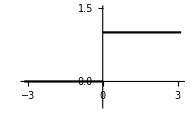

Запишем выражения для коэффициентов Фурье по формулам (2), (3), (4)

Так как функция обращается в ноль при x<0, интегрирование ведем в пределах от 0 до π.

Коэффициент a_0 вычисляется следующим образом:

```mathematica
a0=1/π Integrate[f[x],{x,0,Pi}]
```

1

Коэффициент a_n:

```mathematica
an=1/π Integrate[f[x]Cos[n x],{x,0,Pi}]
```

Sin[n π]/(n π)

При любых n a_n=0, но a_0=1

Коэффициент b_n:

```mathematica
bn=1/π Integrate[f[x]Sin[n x],{x,0,Pi}]
```

(1-Cos[n π])/(n π)

Получили, что коэффициент b_n:

b_n=Piecewise[{{2/((2k+1) π), при n=2k+1}, {0, при n=2k}}]

Запишем ряд Фурье:

f(x)=1/2+∑_(k=0)^∞ (2sin((2k+1)x))/((2k+1)π)

```mathematica
fu[x_,n_]:=1/2+2/π Sum[Sin[(2k+1)x]/(2k+1),{k,0,n}]
```

Получим выражение ряда Фурье до 4-ого члена:

```mathematica
fu[x,4]//Expand
```

1/2+(2 Sin[x])/π+(2 Sin[3 x])/(3 π)+(2 Sin[5 x])/(5 π)+(2 Sin[7 x])/(7 π)+(2 Sin[9 x])/(9 π)

Изобразим графики исходной функции и ряда Фурье до 4ого и до 10ого члена.

```mathematica
Row[{Plot[{fu[x,4],f[x]},{x,-Pi,Pi},ImageSize->300],Plot[{fu[x,10],f[x]},{x,-Pi,Pi},ImageSize->300] }]
```

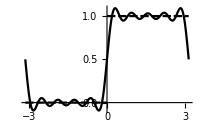
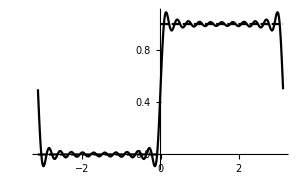

Из графиков видно, что чем больше порядок разложения, тем точнее ряд аппроксимирует функцию.

В данной задаче было показано, как на основе формул для определения коэффициентов Фурье разложить функцию в ряд Фурье.

##### Пример №12.487

Разложить периодическую функцию с периодом 2l функцию в ряд Фурье, построить график.

f(x)=2x ,       0<x<1, 2l=1

Определим заданную функцию, и построим ее график:

```mathematica
f[x_]:=2x
l=1/2;
Plot[f[x],{x,0,1}]
```

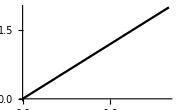

Теперь запишем функции для коэффициентов Фурье по формулам (2), (3), (4):

Так как в формуле (3) при n=0 косинус обращается в единицу, то записывать отдельное выражение для коэффициента a_0 смысла нет.

```mathematica
a[n_]:=Integrate[1/l f[x]Cos[Pi n x/l],{x,0,1}]
b[n_]:=Integrate[1/l f[x] Sin[Pi n x/l],{x,0,1}]
```

Теперь запишем функцию тригонометрического ряда Фурье:

```mathematica
fu[x_,k_]:=a[0]/2+Sum[a[n]Cos[Pi/l n x]+b[n]Sin[Pi/l n x],{n,1,k}]
```

Выведем выражение для ряда до 5ого члена и построим его график:

```mathematica
fu[x,5]
Plot[{Evaluate@fu[x,5],f[x]},{x,0,1}]
```

1-(2 Sin[2 π x])/π-Sin[4 π x]/π-(2 Sin[6 π x])/(3 π)-Sin[8 π x]/(2 π)-(2 Sin[10 π x])/(5 π)

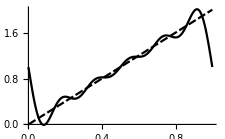

Чтобы оценить верность полученного выражения, найдем сумму ряда:

```mathematica
fu[x,Infinity]
```

1+(ⅈ (-Log[1-ⅇ^(2 ⅈ π x)]+Log[ⅇ^(-2 ⅈ π x) (-1+ⅇ^(2 ⅈ π x))]))/π

Построим график полученной функции:

```mathematica
Plot[{f[x],Evaluate@fu[x,Infinity]},{x,0,1}]
```

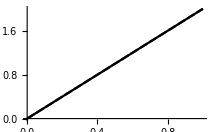

Графики функций совпали, следовательно, как и предполагалось, ряд сходится к функции.

### 7.2. Особенности разложения в ряд Фурье четных и нечетных функций.

Если функцию обладает какой-либо симметрией, то техника разложения в ряд Фурье упрощается.

В случае, если f(x) - четная функция с периодом 2l, то все коэффициенты Фурье b_n равны 0 и, следовательно, в ряде Фурье нет членов с синусами. Тогда получим ряд:

S(x)=a_0/2+∑_(n=1)^∞ a_n cos(π/l n x)

где

a_0=2/l∫_0^l f(x)ⅆx

a_n=2/l∫_0^l f(x)cos(π/l n x)ⅆx

Аналогично в случае, если f(x) - нечетная функция, то все коэффициенты Фурье a_n равны 0 и, следовательно, в ряде Фурье нет членов с косинусами. Тогда получим ряд:

S(x)=∑_(n=1)^∞ b_n sin(π/l n x)

где

b_n=2/l∫_0^l f(x)sin(π/l n x)ⅆx

##### Пример №12.482

Разложить в ряд Фурье функцию:

f(x)=|x|,  -1<x<1, l=1

Запишем заданную функцию:

```mathematica
f[x_]:=Abs[x]
```

Функция четная, значит в разложении будут отсутствовать члены с синусами. Запишем теперь выражение для коэффициента a_n:

```mathematica
a[n_]:=Integrate[2 f[x] Cos[Pi n x],{x,0,1}]
```

Зададим функцию ряда:

```mathematica
fu[x_,k_]:=a[0]/2+Sum[a[n]Cos[Pi n x],{n,1,k}]
```

Выведем полученный ряд до 6ого члена и построим его график:

```mathematica
fu[x,6]
Plot[{f[x],Evaluate@fu[x,6]},{x,-1,1}]
```

1/2-(4 Cos[π x])/π^2-(4 Cos[3 π x])/(9 π^2)-(4 Cos[5 π x])/(25 π^2)

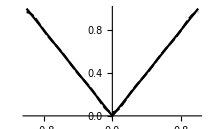

Из графика заключаем, что ряд сходится к функции.

##### Пример №12.493

Доопределяя необходимым образом заданную в промежутке функцию до периодической, получить для нее: а) ряд Фурье по косинусам; б) ряд Фурье по синусам.

f(x)=e^x, 0<x<ln 2

Для того чтобы получить ряд Фурье по косинусам, необходимо чтобы функция была чётной. Функция e^(|x|) удовлетворяет данному требованию. Запишем и изобразим эту функцию:

```mathematica
f[x_]:=Exp[Abs[x]]
Plot[f[x],{x,-Log[2],Log[2]}]
```

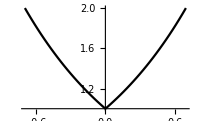

Теперь получим выражение для коэффициента Фурье и запишем ряд:

```mathematica
a[n_]:=Integrate[2/Log[2] f[x]Cos[Pi/Log[2] n x],{x,0,Log[2]}]
fu[x_,k_]:=a[0]/2+Sum[a[n]Cos[Pi/Log[2] n x],{n,1,k}]
```

Изобразим полученный ряд:

```mathematica
fu[x,5]
Plot[{f[x],Evaluate@fu[x,5]},{x,-Log[2],Log[2]}]
```

1/Log[2]-(6 Cos[(π x)/Log[2]] Log[2])/(π^2+Log[2]^2)-(6 Cos[(3 π x)/Log[2]] Log[2])/(9 π^2+Log[2]^2)-(6 Cos[(5 π x)/Log[2]] Log[2])/(25 π^2+Log[2]^2)+(Cos[(2 π x)/Log[2]] Log[4])/(4 π^2+Log[2]^2)+(Cos[(4 π x)/Log[2]] Log[4])/(16 π^2+Log[2]^2)

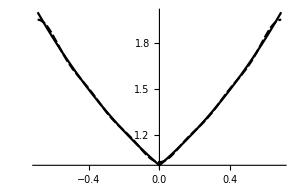

Теперь, для того чтобы получить разложение Фурье по синусам, доопределим исходную функцию до нечетной следующим образом:

f(x)=Piecewise[{{e^x, 0<x<ln 2}, {-e^-x, -ln 2<x<0}}]

Запишем и построим полученную функцию:

```mathematica
f[x_]:=Piecewise[{{Exp[x],Log[2]>x>0},{-Exp[-x],-Log[2]<x<0}}]
Plot[f[x],{x,-Log[2],Log[2]}]
```

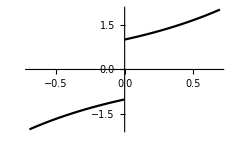

Запишем выражения для коэффициента b_n и ряда:

```mathematica
b[n_]:=Integrate[2/Log[2] f[x]Sin[Pi/Log[2] n x],{x,0,Log[2]}]
fu[x_,k_]:=Sum[b[n]Sin[Pi/Log[2] n x],{n,1,k}]
```

Получим разложение функции до 6ого члена и построим его график:

```mathematica
fu[x,6]
Plot[{f[x],Evaluate@fu[x,12]},{x,-Log[2],Log[2]}]
```

(6 π Sin[(π x)/Log[2]])/(π^2+Log[2]^2)-(4 π Sin[(2 π x)/Log[2]])/(4 π^2+Log[2]^2)+(18 π Sin[(3 π x)/Log[2]])/(9 π^2+Log[2]^2)-(8 π Sin[(4 π x)/Log[2]])/(16 π^2+Log[2]^2)+(30 π Sin[(5 π x)/Log[2]])/(25 π^2+Log[2]^2)-(12 π Sin[(6 π x)/Log[2]])/(36 π^2+Log[2]^2)

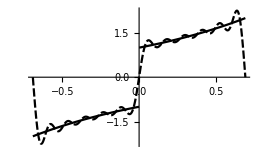

В точке разрыва значение ряда S(0) будет равно:

S(0)=(f(+0)+f(-0))/2

##### Программный модуль

Проанализировав последовательность действий в общем случае, напишем простую обучающую программу, которая будет раскладывать функцию в ряд Фурье на заданном интервале [h;g] с полупериодом l=(g-h)/2:

```mathematica
fourier[x_,func_,h_,g_,k_]:=Module[{a,b,l},
l=(g-h)/2;
a[n_]:=Integrate[1/l func Cos[Pi n x/l],{x,h,g}];
b[n_]:=Integrate[1/l func  Sin[Pi n x/l],{x,h,g}];
a[0]/2+Sum[a[n]Cos[Pi/l n x]+b[n]Sin[Pi/l n x],{n,1,k}]]
```

Проведем графическую проверку полученного модуля:

##### Пример №12.483

Разложить в ряд Фурье функцию:

f(x)=|cos(x)|,  -π<x<π, l=π

Зададим функцию ряда через написанный нами модуль:

```mathematica
fu[x_,k_]:=fourier[x,Abs[Cos[x]],-Pi,Pi,k]
```

Теперь выведем разложение до 8-ого члена и построим график:

```mathematica
fu[x,8]
Plot[{Abs[Cos[x]],Evaluate@fu[x,8]},{x,-Pi,Pi}]
```

2/π+(4 Cos[2 x])/(3 π)-(4 Cos[4 x])/(15 π)+(4 Cos[6 x])/(35 π)-(4 Cos[8 x])/(63 π)

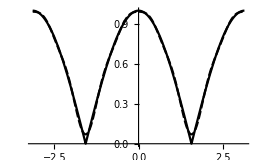

При увеличении порядка разложения ряд будет сходиться к функции.

##### Пример №12.488

Разложить в ряд Фурье функцию:

f(x)=10-x,  5<x<15, l=5

```mathematica
fu[x_,k_]:=fourier[x,10-x,5,15,k]
```

```mathematica
fu[x,8]
Plot[{10-x,Evaluate@fu[x,8]},{x,5,15}]
```

-(10 Sin[(π x)/5])/π+(5 Sin[(2 π x)/5])/π-(10 Sin[(3 π x)/5])/(3 π)+(5 Sin[(4 π x)/5])/(2 π)-(2 Sin[π x])/π+(5 Sin[(6 π x)/5])/(3 π)-(10 Sin[(7 π x)/5])/(7 π)+(5 Sin[(8 π x)/5])/(4 π)

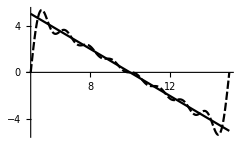

Разобрав два примера, будем считать, что написанный модуль проверку прошел.

### 7.3. Ряд Фурье в комплексной форме.

Применим тождества Эйлера для косинуса и синуса ряда (1):

S(t)=a_0/2+∑_(n=1)^∞ (a_n cos(n t)+b_n sin(n t))=a_0/2+∑_(n=1)^∞ (a_n(e^(i n t)+e^(- i n t))/2+b_n(e^(i n t)- e^(-i n t))/(2i))=
=a_0/2+∑_(n=1)^∞ (a_n(e^(i n t)+e^(- i n t))/2-i b_n(e^(i n t)- e^(-i n t))/2)=a_0/2+∑_(n=1)^∞ ((a_n-i b_n)/2 e^(i n t)+(a_n+i b_n)/2 e^(-i n t))

Введем коэффициенты a_n и b_n  с отрицательными номерами:

a_-n=a_n
b_-n=b_n

Для которых также справедливы формулы:

a_-n=1/π∫_-π^π f(t)cos(-n t)ⅆt=1/π∫_-π^π f(t)cos(n t)ⅆt=a_n
b_-n=1/π∫_-π^π f(t)sin(-n t)ⅆt=-1/π∫_-π^π f(t)sin(n t )ⅆt=-b_n

Продолжим преобразование:

f(t)=a_0/2+∑_(n=1)^∞ (a_n-i b_n)/2 e^(i n t)+∑_(n=-∞)^-1 (a_n-i b_n)/2 e^(i n t)=∑_(n=-∞)^∞ (a_n-i b_n)/2 e^(i n t)

Обозначим:

c_n=(a_n-i b_n)/2=1/(2π)∫_-π^π f(t)cos(n t)ⅆt-i 1/(2π)∫_-π^π f(t)sin(n t)ⅆt=1/(2π)∫_-π^π f(t)e^(-n t)ⅆt

Итак, в комплексной форме ряд Фурье для функции с произвольным полупериодом l записывается:

f(t)=∑_(n=-∞)^∞ c_n ⅇ^((ⅈ n π x)/l)

c_n=1/(2l)∫_-l^l f(t)ⅇ^(-(ⅈ n π t)/l)ⅆt

##### Пример №12.484

Представить функцию в виде ряда Фурье в комплексной форме:

f(t)=t^2, -π<t<π, l=π

Запишем функцию:

```mathematica
f[t_]:=t^2
```

Используя формулу (13), запишем коэффициент c_n:

```mathematica
c[n_]:=Integrate[1/(2Pi)f[t] Exp[-I n t],{t,-Pi,Pi}]
```

Запишем функцию ряда Фурье до k-ого порядка:

```mathematica
fu[t_,k_]:=Sum[c[n]Exp[I n t],{n,-k,k}]
```

Получим выражение ряда до 4-ого порядка:

```mathematica
fu[t,4]
```

-2 ⅇ^(-ⅈ t)-2 ⅇ^(ⅈ t)+1/2 ⅇ^(-2 ⅈ t)+1/2 ⅇ^(2 ⅈ t)-2/9 ⅇ^(-3 ⅈ t)-2/9 ⅇ^(3 ⅈ t)+1/8 ⅇ^(-4 ⅈ t)+1/8 ⅇ^(4 ⅈ t)+π^2/3

Сравним данный результат, преобразовав его при помощи функции ExpToTrig, с тем, что бы у нас получилось, если бы мы воспользовались модулем fourier:

```mathematica
fourier[t,f[t],-Pi,Pi,4]
fu[t,4]//ExpToTrig
```

π^2/3-4 Cos[t]+Cos[2 t]-4/9 Cos[3 t]+1/4 Cos[4 t]

π^2/3-4 Cos[t]+Cos[2 t]-4/9 Cos[3 t]+1/4 Cos[4 t]

Как и ожидалось, ответы совпадают.

Построим график, чтобы убедиться, что ряд сходится к исходной функции:

```mathematica
Plot[{f[t],Evaluate@fu[t,4]},{t,-Pi,Pi}]
```

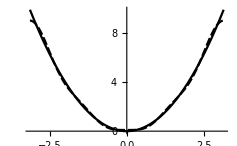

##### Программный модуль

Подобно модулю разложения в тригонометрический ряд составим модуль разложения в ряд Фурье в комплексной форме:

```mathematica
fourierC[t_,func_,h_,g_,k_]:=Module[{c,l},
l=(g-h)/2;
c[n_]:=1/(2l)Integrate[func Exp[- I Pi/l n t],{t,h,g}];
Sum[c[n]Exp[I Pi/l n t],{n,-k,k}]]
```

##### Пример №12.486

Представить функцию в виде ряда Фурье в комплексной форме:

f(t)=|sin(t)|, -π<t<π, l=π

Выведем результат работы функции fourierC и построим графики исходной функции и полученного ряда:

```mathematica
fourierC[t,Abs[Sin[t]],-Pi,Pi,4]
Plot[{Abs[Sin[t]],Evaluate@fourierC[t,Abs[Sin[t]],-Pi,Pi,4]},{t,-Pi,Pi}]
```

2/π-(2 ⅇ^(-2 ⅈ t))/(3 π)-(2 ⅇ^(2 ⅈ t))/(3 π)-(2 ⅇ^(-4 ⅈ t))/(15 π)-(2 ⅇ^(4 ⅈ t))/(15 π)

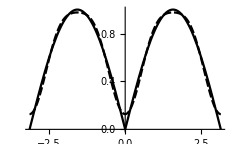

Будем считать, что проверка прошла успешно.

### 7.4. Системные функции разложения в ряд Фурье.

Mathematica имеет встроенные функции разложения в ряд Фурье. Рассмотрим на примере:

##### Пример №12.484

Разложить функцию в ряд Фурье периода l:

f(x)=x^2, -π<x<π, l=π

Для решения данной задачи воспользуемся встроенной функцией FourierSeries, имеющей следующую структуру: FourierSeries[expr,t,n] , где expr - выражение или функция, которую требуется разложить в ряд Фурье, t - переменная, по которой ведется разложение, n - порядок разложения.

Запишем исходную функцию:

```mathematica
f[x_]:=x^2
```

Теперь получим разложение в ряд до 6ого члена.

```mathematica
FourierSeries[x^2,x,6]
```

-2 ⅇ^(-ⅈ x)-2 ⅇ^(ⅈ x)+1/2 ⅇ^(-2 ⅈ x)+1/2 ⅇ^(2 ⅈ x)-2/9 ⅇ^(-3 ⅈ x)-2/9 ⅇ^(3 ⅈ x)+1/8 ⅇ^(-4 ⅈ x)+1/8 ⅇ^(4 ⅈ x)-2/25 ⅇ^(-5 ⅈ x)-2/25 ⅇ^(5 ⅈ x)+1/18 ⅇ^(-6 ⅈ x)+1/18 ⅇ^(6 ⅈ x)+π^2/3

Как мы видим, по умолчанию Mathematica раскладывает в ряд в комплексной форме. Также мы можем перейти к более привычной для нас, тригонометрической, форме:

```mathematica
FourierSeries[x^2,x,6]//ExpToTrig
```

π^2/3-4 Cos[x]+Cos[2 x]-4/9 Cos[3 x]+1/4 Cos[4 x]-4/25 Cos[5 x]+1/9 Cos[6 x]

или же можем просто воспользоваться функцией FourierTrigSeries:

```mathematica
FourierTrigSeries[x^2,x,6]
```

π^2/3+4 (-Cos[x]+1/4 Cos[2 x]-1/9 Cos[3 x]+1/16 Cos[4 x]-1/25 Cos[5 x]+1/36 Cos[6 x])

Как мы видим, функция - четная, а функции синуса в разложении отсутствуют.

Найдем формулу n-ого коэффициента при помощи функции FourierCoefficient:

```mathematica
FourierCoefficient[x^2,x,n]
```

(2 (-1)^n)/n^2

Напоминаем, что это коэффициент разложения в комплексной форме с_n, и он не равен коэффициентам a_n или b_n.

Так же находим и свободный коэффициент:

```mathematica
FourierCoefficient[x^2,x,0]
```

π^2/3

Составим функцию ряда:

```mathematica
fu[x_,n_]:=FourierSeries[t^2,t,n]/.t-> x
```

```mathematica
fu[x,6]//ExpToTrig
```

π^2/3-4 Cos[x]+Cos[2 x]-4/9 Cos[3 x]+1/4 Cos[4 x]-4/25 Cos[5 x]+1/9 Cos[6 x]

Покажем графики  исходной функции и ряда Фурье до 5ого порядка:

```mathematica
Plot[{f[x],Evaluate@fu[x,5]},{x,-Pi,Pi}]
```

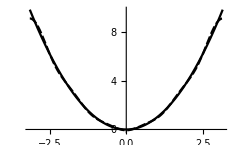

##### Пример №12.496

Доопределяя необходимым образом заданную в промежутке функцию до переодической, получить для нее: а) ряд Фурье по косинусам б) ряд Фурье по синусам.

f(x)=x sin(x), 0<x<π

Так как данная функция - четная, получим выражение ряда в общей форме.

Для этого запишем и построим график заданной функции:

```mathematica
f[x_]:=x Sin[x]
Plot[f[x],{x,-Pi,Pi}]
```

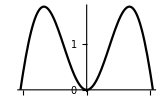

Так как данная функция - четная, в разложении будут отсутствовать члены с синусом. Тогда:

c_n=(a_n-i b_n)/2=(a_n-i 0)/2⇒a_n=2 c_n

Получим выражение для нулевого и n-ого коэффициента:

```mathematica
FourierCoefficient[f[x],x,n]
```

(-1)^(1+n)/(-1+n^2)

Отсюда следует, что

a_n=(2(-1)^(n+1))/(n^2-1)

Найдем значение коэффициента при n=1:

```mathematica
FourierCoefficient[f[x],x,1]
```

-1/4

Теперь можем записать ряд в виде:

f(x)=1-1/2 cos(x)+∑_(n=2)^∞ (2(-1)^(n+1))/(n^2-1)cos(n x)

Ряд Фурье по синусам для исходной функции получим при помощи встроенной опции FourierSinSeries (существует аналогичная опция FourierCosSeries),  она имеет ту же структуру, что и FourierSeries:

```mathematica
FourierSinSeries[f[x],x,8]
```

1/2 π Sin[x]-(16 Sin[2 x])/(9 π)-(32 Sin[4 x])/(225 π)-(48 Sin[6 x])/(1225 π)-(64 Sin[8 x])/(3969 π)

Изобразим график функции и ряда:

```mathematica
Plot[{f[x],Evaluate@FourierSinSeries[f[x],x,8]},{x,-Pi,Pi}]
```

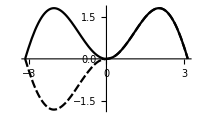

Как видно из графика, исходная функция была доопределена до несимметричной функции, у которой отсутствует косинус в разложении в ряд.

Коэффициент b_n получим при помощи функции FourierSinCoefficient:

```mathematica
FourierSinCoefficient[f[x],x,n]
```

-(4 (1+(-1)^n) n)/((-1+n^2)^2 π)

а также коэффициент b_1:

```mathematica
FourierSinCoefficient[f[x],x,1]
```

π/2

В итоге, ряд записывается в виде:

f(x)=π/2 sin(x)-4/π∑_(n=2)^∞ ((1+(-1)^n) n)/((-1+n^2)^2)sin(n x)

### 7.5. Интеграл Фурье. Преобразование Фурье.

Пусть функция f(x):

1) Абсолютно интегрируема на ℝ, т.е. сходится интеграл: ∫_(-∞)^(+∞) |f(x)|𝕕 x;

2) Кусочно гладкая на каждом конечном отрезке действительной оси.

Тогда справедлива интегральная формула Фурье:

(f(x+0)-f(x-0))/2=1/π∫_0^∞ 𝕕 ω∫_(-∞)^∞ f(t)cosω(x-t)ⅆt

Чтобы показать аналогию интеграла Фурье и ряда Фурье, проведем некоторые преобразования:

f(x)=1/π∫_0^∞ 𝕕 ω∫_(-∞)^∞ f(t)(cos ω t cos ω x + sin ω t sin ω x)ⅆt=
=1/π∫_0^∞ (∫_(-∞)^∞ f(t)cos ω tⅆt )cos ω x +(∫_(-∞)^∞ f(t) sin ω tⅆt )sin ω x 𝕕 ω

Введя обозначения:

A(ω)=∫_(-∞)^∞ f(t)cos ω tⅆt , B(ω)=∫_(-∞)^∞ f(t) sin ω tⅆt

Получаем:

f(x)=1/π∫_0^∞ A(ω)cos ω x +B(ω)sin ω x 𝕕 ω

В этом случае, в отличии от тригонометрического ряда Фурье, частота ω изменяется не дискретно, а непрерывно. И наиболее важным отличием является то, что в виде интеграла Фурье можно представить и непериодическую функцию.

Как и ряд Фурье, интеграл Фурье имеет комплексную форму записи.

Так как внутренний интеграл в выражении (14) функция четная, тогда:

1/π∫_0^∞ 𝕕 ω∫_(-∞)^∞ f(t)cos ω(x-t)ⅆt=1/(2π)∫_(-∞)^∞ 𝕕 ω∫_(-∞)^∞ f(t)cos ω(x-t)ⅆt

Так как:

∫_(-∞)^∞ f(t)sin ω(x-t)ⅆt- нечетная функция от ω, то ⅈ/(2π)∫_(-∞)^∞ 𝕕 ω∫_(-∞)^∞ f(t)sin ω(x-t)ⅆt=0

Тогда:

f(x)=1/(2π)∫_(-∞)^∞ 𝕕 ω∫_(-∞)^∞ f(t)(cos ω(x-t)+ⅈ sin ω(x-t))ⅆt=1/(2π)∫_(-∞)^∞ 𝕕 ω∫_(-∞)^∞ f(t)ⅇ^(ⅈ ω (x-t))ⅆt=

=1/(√(2π))∫_(-∞)^∞ ⅇ^(ⅈ ω x)(1/(√(2π))∫_(-∞)^∞ f(t)ⅇ^(-ⅈ ω t)ⅆt)𝕕 ω

Функция:

S(ω)= 1/(√(2π))∫_(-∞)^∞ f(t)ⅇ^(-ⅈ ω t)ⅆt

Называется прямым преобразованием Фурье функции f(x). Преобразованием Фурье также называют отображение f(x)⟶ S(ω), которое задается формулой (17). Обратное отображение называется обратным преобразованием Фурье, и задается формулой:

f(x)=1/(√(2π))∫_(-∞)^∞ ⅇ^(ⅈ ω x)S(ω) 𝕕 ω

Комплекснозначная функция S(ω) называется также спектральной плотностью функции f(x) и несет в себе значительную информацию о функции f(x).

Если функция f(x) четная, интегральную формулу (18) можно записать так:

f(x)=∫_0^∞ A(ω)cos ω x 𝕕 ω=2/π∫_0^∞ (∫_0^∞ f(t)cos ω tⅆt)cos ω x 𝕕 ω

Обозначим:

f^*( ω)=√(2/π) ∫_0^∞ f(t)cos ω tⅆt

Тогда получим:

f(x)=√(2/π)∫_0^∞ f^*(ω) cos ω x 𝕕 ω

Функция f^*(ω) называется косинус-преобразованием Фурье функции f(x).

Аналогично, если f(x) - нечетная, то можно рассмотреть синус-преобразование:

f_*( ω)=√(2/π) ∫_0^∞ f(t)sin ω tⅆt

f( x)=√(2/π) ∫_0^∞ f_*( ω) sin ω tⅆt

##### Пример №1

Найти преобразование Фурье функции и представить ее интегралом Фурье в комплексной форме:

f(x)=x ⅇ^(- |x|)

Запишем исходную функцию:

```mathematica
f[x_]:=x Exp[- Abs[x]]
```

Найдем преобразование Фурье по формуле (17):

```mathematica
Integrate[1/(√(2π))t Exp[-Abs[t]]Exp[-I w t],{t,-Infinity,Infinity},Assumptions->1>  Im[w]>-1]
```

-(2 ⅈ √(2/π) w)/((-ⅈ+w)^2 (ⅈ+w)^2)

Будем обозначать преобразование Фурье по формуле (17) ℱ[f].

Получили, что спектральная функция имеет вид:

ℱ[f]=S(ω)=-√(1/(2π))(4 ⅈ  ω)/((ω^2+1)^2)

Значит функцию f(x) можно представить в виде:

f(x)=x ⅇ^(-|x|)=1/(√(2π))∫_(-∞)^∞ -√(1/(2π))(4 ⅈ  ω)/((ω^2+1)^2)ⅇ^(ⅈ ω x)ⅆω=-(2i)/π∫_(-∞)^∞ ω/((ω^2+1)^2)ⅇ^(ⅈ ω x)ⅆ ω

##### Пример №12.515

Найти преобразование Фурье функции и представить ее интегралом Фурье в комплексной форме:

f(t)=Piecewise[{{cos a t, |t|<π/a}, {0, else}}], a>0

Запишем функцию:

```mathematica
f[t_]:=Piecewise[{{Cos[a t],Abs[t]<Pi/a}},0]
```

Построим ее график при a=1:

```mathematica
Plot[f[t]/.a->1,{t,-2Pi,2Pi}]
```

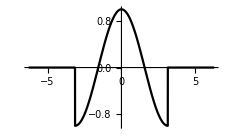

В Wolfram Mathematica существует целый ряд функций для работы с преобразованием Фурье. Рассмотрим две основные функции: FourierTransform и InverseFourierTransform. Внутри системы они определены следующим образом:

FourierTransform[f(t),t,ω] :   ℱ[f]= S(ω)= √((|b|)/(2π)^(1-a))∫_(-∞)^∞ f(t) e^(i b ω t)dt.

InverseFourierTransform[S(ω),ω,t] :  ℱ^-1[f]=  f(t)= √((|b|)/(2π)^(1+a))∫_(-∞)^∞ F(ω) e^-ibωt dω.

где {a,b} - параметры Фурье (FourierParameters).

В соответствии с данным нами определением отображения Фурье (17) параметры {a,b} = {0,-1}. Однако, по умолчанию в системе Mathematica {a,b}={0,1}. Для того чтобы изменить их стандартное значение, воспользуемся функцией SetOptions:

```mathematica
SetOptions[FourierTransform,FourierParameters-> {0,-1}];
SetOptions[InverseFourierTransform, FourierParameters-> {0,-1}];
```

Итак, для того чтобы найти спектральную плотность заданной функции f(t), воспользуемся опцией FouirierTransform:

```mathematica
Evaluate@FourierTransform[f[t],t,w,Assumptions-> a>0]
```

(√(2/π) w Sin[(π w)/a])/(a^2-w^2)

Такой же результат мы получим, интегрируя функцию по формуле (17):

```mathematica
Integrate[1/(√(2Pi))f[t] Exp[- I w t],{t,-Infinity,Infinity},Assumptions->a>0]
```

-(√(2/π) w Sin[(π w)/a])/(-a^2+w^2)

Получили следующий результат:

ℱ[f]=S(ω)=(√(2/π) ω Sin[(π ω)/a])/(a^2-ω^2)

Значит теперь можно представить исходную функцию в виде:

f(t)=1/(√(2π))∫_(-∞)^∞ (√(2/π) ω Sin[(π ω)/a])/(a^2-ω^2)ⅇ^(ⅈ ω t)ⅆω=1/π∫_(-∞)^∞ (ω Sin[(π ω)/a])/(a^2-ω^2)ⅇ^(ⅈ ω t)ⅆω

##### Пример №12.517

Найти пару косинус- или синус- преобразований указанной функции:

f(t)=1/(a^2+t^2),a>0.

Так как данная функция четная, воспользуемся формулой (19), для того чтобы найти косинус-преобразование исходной функции:

```mathematica
Integrate[√(2/Pi)1/(a^2+t^2)Cos[w t],{t,0,Infinity},Assumptions->a>0]
```

ConditionalExpression[(ⅇ^(-a Abs[w]) √(π/2))/a,w∈Reals]

При условии, что ω принадлежит множеству действительных чисел, получили:

f^*(ω)=√(π/2)ⅇ^(-a |ω|)/a

Тогда заданную функцию можно записать в виде:

f(t)=1/a∫_0^∞ ⅇ^(-a ω)cos(ω t)ⅆω

Разумеется, Wolfram Mathematica предоставляет удобные опции FourierCosTransform и FourierSinTransform для нахождения косинус- и синус преобразований Фурье.

##### Пример №12.518

Найти пару косинус- или синус- преобразований указанной функции:

f(t)=t/(a^2+t^2),a>0.

Так как исходная функция нечетная, воспользуемся функцией FourierSinTransofrm:

```mathematica
FourierSinTransform[t/(a^2+t^2),t,w,Assumptions->a>0]
```

ⅇ^(-a w) √(π/2)

Получили, что:

f_*(ω)=ⅇ^(-a ω) √(π/2)
f(t)=∫_0^∞ ⅇ^(-a ω)sin(ω t)ⅆω

### 7.6. Свойства преобразования Фурье

Пусть функциям f(t), g(t) соответствуют преобразования Фурье F(ω),G(ω). Тогда запишем основные свойства Фурье-преобразования (без доказательств):

1. Линейность

ℱ[a f(t)+b g(t)]=a F(ω)+b G(ω)

2. Запаздывание

ℱ[f(t-a)]=ⅇ^(-ⅈ ω a)F(ω)

3. Частотный сдвиг

ℱ[ⅇ^(- ⅈ a t)f(t)]=F(ω-a)

4. Масштабирование

ℱ[f(a t)]=1/(|a|)F(ω/a)

5. Преобразование Фурье n-ой производной

ℱ[ⅆ^n/(ⅆ t^n)f(t)]=(ⅈ ω)^n F(ω)

6. Дифференцирование изображения

ℱ[t^n f(t)]=ⅈ^n ⅆ^n/(ⅆ ω^n)F(ω)

7. Преобразование свертки

ℱ[(f*g)(t)]=√(2π)F(ω)G(ω)

8. Преобразование произведения

ℱ[f(t)g(t)]=1/(√(2π))(F*G)(ω)

9. Преобразование дельта-функции Дирака

ℱ[δ(t)]=1/(√(2π))

10. Преобразование константы

ℱ[a]=a √(2π)δ(t)

11. Преобразование многочленов:

ℱ[t^n]=ⅈ^n √(2π)δ^(n)(ω)
где n- натуральное число, δ^(n)(ω)- n-я обобщенная производная дельта-функции.

12. Изображения некоторых функций:

ℱ[ⅇ^(- ⅈ a t)]=√(2π)δ(ω-a)

ℱ[cos(a t)]=√(2π)(δ(ω-a)+δ(ω+a))/2

ℱ[sin(a t)]=√(2π)(δ(ω-a)-δ(ω+a))/(2ⅈ)

ℱ[ⅇ^(- a t^2)]=1/(√(2a))ⅇ^(-ω^2/4a)

ℱ[ⅇ^(- t^2/2)]=ⅇ^(-ω^2/2) -  функция Гаусса совпадает со своим изображением

ℱ[1/t]=-ⅈ √(π/2)sign(ω)

ℱ[1/t^n]=-ⅈ √(π/2)(-ⅈ ω)^(n-1)/((n-1)!)sign(ω)

ℱ[sign(t)]=√(2/π)(- ⅈ ω)^-1

ℱ[√(2π)H(t)]=1/(ⅈ ω)+π δ(ω)
H(t)- функция Хевисайда.

Рассмотрим несколько тривиальных примеров применения данных свойств.

##### Пример №1

Найти изображение многочлена:

P_5(t)=24 t^5-3 t^4+11 t^2-t+2

Применив свойства 1 и 11, получаем следующий результат:

ℱ[24 t^5-3 t^4+11 t^2-t+2]=24ℱ[t^5]-3ℱ[t^4]+11ℱ[t^2]-ℱ[t]+2ℱ[1]=
=√(2π)(24 ⅈ^5 δ^(5)(ω)-3 ⅈ^4 δ^(4)(ω)-11 ⅈ^2 δ''(ω)-ⅈδ'(ω)+2δ(ω))=
=√(2π)(24ⅈ δ^(5)(ω)-3δ^(4)(ω)+11δ''(ω)-ⅈ δ'(ω)+2δ(ω))

Тот же результат получим при помощи FourierTransform:

```mathematica
FourierTransform[24 t^5-3 t^4+11 t^2-t+2,t,w]//TraditionalForm
```

2 √(2 π) w-ⅈ √(2 π) δ'(w)-11 √(2 π) δ''(w)-3 √(2 π) δ^(4)(w)+24 ⅈ √(2 π) δ^(5)(w)

##### Пример №2

Найти изображение дифференциального выражения:

x''+2x'+x=sin(t)

Обозначим ℱ[x(t)]=X(ω).Тогда согласно свойству 5 имеем:

ℱ[x''+2x'+x-ⅇ^-t]=ℱ[x'']+2ℱ[x']+ℱ[x]-ℱ[sin(t)]=
=(ⅈ ω)^2 X+2(i ω)X+X-√(2π)(δ(ω-1)-δ(ω+1))/(2ⅈ)

Отсюда видно, что:

- ω^2X+2i ω X+X=√(2π)(δ(ω-1)-δ(ω+1))/(2ⅈ)
X=√(2π)(δ(ω-1)-δ(ω+1))/(2ⅈ)
X(ω)=√(2π)(δ(ω-1)-δ(ω+1))/(2ⅈ(-ω^2+2i ω+1))

Найдем функцию x(t):

```mathematica
InverseFourierTransform[√(2π)(DiracDelta[(ω-1)]-DiracDelta[(ω+1)])/(2I(-ω^2+2I ω+1)),ω,t]
```

-Cos[t]/2

Получается, что частное решение исходного дифференциального уравнения:

x(t)=-1/2cos(t)

##### Пример №3

Зная изображение функции f(t), найти изображение функции g(t):

ℱ[1/(a^2+t^2)]=√(π/2)ⅇ^(-a ω)/a,g(t)=t^4/(a^2+t^2)

Согласно свойству 6 имеем:

t^4/(a^2+t^2)=t^4 f(t),    ℱ[t^4 f(t)]=ⅈ^4 ⅆ^4/(ⅆ ω^4)ℱ[f(t)]
ℱ[t^4/(a^2+t^2)]=√(π/2)ⅆ^4/(ⅆ ω^4)(ⅇ^(-a ω)/a)

Найдем производную 4-ого порядка:

```mathematica
D[Exp[-a w]/a,{w,4}]
```

a^3 ⅇ^(-a w)

В итоге, получаем ответ:

ℱ[t^4/(a^2+t^2)]=√(π/2)a^3 ⅇ^(-a ω)

### 7.7. Связь коэффициентов ряда Фурье с коэффициентами ряда Лорана.

Пусть функция f(z) регулярна в кольце r_1< |z|<1+r_2 (0≤ r_1<1, r_2>0) содержащем единичную окружность |z|=1. Тогда она представляется в этом кольце рядом Лорана:

f(z)=∑_(n=-∞)^∞ c_n z^n

Откуда, полагая z=ⅇ^(i ϕ), получаем разложения в ряд Фурье функции:

F(ϕ)=f(ⅇ^iϕ)=∑_(n=-∞)^∞ c_n ⅇ^(ⅈ ϕ n)

Отсюда следует обратное: если функция F(ϕ) представляется в виде: F(ϕ)=f(ⅇ^(ⅈ ϕ)) , где функция f(z) регулярна в кольце, то ряд (43) является рядом Фурье для F(ϕ).

##### Пример №12.352

Найти все разложения указанных функций в ряды Лорана по степеням z-z_0.

f(z)=1/(z(z-1)),z_0=1

Запишем функцию:

```mathematica
f[z_]:=1/(z(z-1))
```

Как уже можно было заметить, Mathematica не предоставляет встроенных средств для разложения функций в ряд Лорана. В ней есть только функция Series, которая находит разложение в ряд лишь в окрестности точки z_0.

Однако, благодаря связи ряда Лорана и Фурье, а также тому, что Mathematica имеет целый ряд функций для работы с рядами Фурье, можно составить алгоритм разложения функции в ряд Лорана через ряд Фурье.

Изобразим особые точки функции f(z), выберем контур С, составим множество коэффициентов ряда Фурье для этого контура, и затем сформируем из них ряд Лорана.

```mathematica
Graphics[{Circle[{1,0},1/2],Circle[{1,0},3/2],Text["r_1",{1/2,1/2}],Text["r_2",{3/2,3/2}],PointSize[Large],Point[ReIm[z/.Solve[f[z]^-1==0,z]]]},PlotRange->{{-3,3},{-3,3}},Frame->False,Axes->True,AxesLabel->{Re,Im}]
```

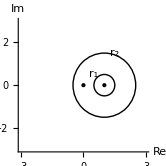

Найдем коэффициенты ряда Лорана при 0< |z-1|<1 . Для этого выберем контур r_1 и воспользуемся функцией FourierCoefficient.

Выберем, к примеру, r_1=1/2. Тогда получим замену: z-z_0=r ⅇ^(ⅈ t), z=z_0+r ⅇ^(ⅈ t)

```mathematica
Table[FourierCoefficient[f[1+1/2 Exp[I t]],t,n]/(1/2)^n,{n,1,10}]
```

{1,-1,1,-1,1,-1,1,-1,1,-1}

Примечание: действие деления на r^n следует из следующего: заменив z=r ⅇ^(ⅈ t) получаем, что f(r ⅇ^(ⅈ t))=∑_(-∞)^∞ c_n r^n ⅇ^(ⅈ n t), тогда, чтобы получить c_n- коэффициент Лорана, необходимо разделить получившийся коэффициент Фурье на r^n.

Составим ряд Лорана вида:

f(z)=∑_(n=-k)^k (c_n(z-z_0))^n

```mathematica
lor[z_,k_,r_]:=Sum[Evaluate[FourierCoefficient[f[1+r Exp[I t]],t,n]]/(r)^n (z-1)^n,{n,-k,k}]
```

```mathematica
lor[z,8,1/2]
```

-2+1/(-1+z)-(-1+z)^2+(-1+z)^3-(-1+z)^4+(-1+z)^5-(-1+z)^6+(-1+z)^7-(-1+z)^8+z

Теперь можно найти разложение функции в кольце |z-1| >1:

```mathematica
lor[z,8,3]
```

1/(-1+z)^8-1/(-1+z)^7+1/(-1+z)^6-1/(-1+z)^5+1/(-1+z)^4-1/(-1+z)^3+1/(-1+z)^2

Сравним получившиеся ответы с тем, что получается при использовании функции loranO (из Главы 2 Параграфа 5):

```mathematica
loranO[z,1/(z(z-1)),1,1/2,8]
loranO[z,1/(z(z-1)),1,3,8]
```

-2+1/(-1+z)-(-1+z)^2+(-1+z)^3-(-1+z)^4+(-1+z)^5-(-1+z)^6+(-1+z)^7-(-1+z)^8+z

1/(-1+z)^8-1/(-1+z)^7+1/(-1+z)^6-1/(-1+z)^5+1/(-1+z)^4-1/(-1+z)^3+1/(-1+z)^2

Получили такие же ответы.

##### Программный модуль

Опыт, полученный в предыдущем примере, используем для составления программного модуля:

```mathematica
loranFC[expr_,{z_,z0_,k_},r_]:=Module[{c},
c[n_]:=FourierCoefficient[expr/.z->z0+r Exp[I t],t,n]/(r)^n;
Sum[c[n](z-z0)^n,{n,-k,k}]]
```

Продемонстрируем пример:

```mathematica
loranFC[1/(z(z-1)),{z,1,8},3]
```

1/(-1+z)^8-1/(-1+z)^7+1/(-1+z)^6-1/(-1+z)^5+1/(-1+z)^4-1/(-1+z)^3+1/(-1+z)^2

Сравним время работы получившегося алгоритма и алгоритма, работающего на основе вычетов (из Главы 2 Параграфа 6):

```mathematica
t1=Timing[loranFC[1/(z(z-1)),{z,1,8},3]]
t2=Timing[loranR[1/(z(z-1)),{z,1,8},3]]
```

{17.4063,1/(-1+z)^8-1/(-1+z)^7+1/(-1+z)^6-1/(-1+z)^5+1/(-1+z)^4-1/(-1+z)^3+1/(-1+z)^2}

{0.03125,1/(-1+z)^8-1/(-1+z)^7+1/(-1+z)^6-1/(-1+z)^5+1/(-1+z)^4-1/(-1+z)^3+1/(-1+z)^2}

```mathematica
t1[[1]]/t2[[1]]
```

557.

Как мы видим, алгоритм на основе вычетов работает почти в 600 раз быстрее. Поэтому в дальнейшем использовать  метод на основе ряда Фурье для разложения функций в ряд Лорана не будем.

### 7.8. Ядро Дирихле. Интеграл Дирихле.

Введем обозначения: A_n(x)=a_n cos(n x)+b_n sin(n x), где a_n,b_n- коэффициенты Фурье

A_n(x)=a_n cos(n x)+b_n sin(n x),где a_n,b_n- коэффициенты Фурье
S_n(x)=∑_(k=0)^n A_k(x) -частичные суммы ряда Фурье
σ(x)=∑_(k=0)^∞ A_k(x)- ряд Фурье

Запишем частичную сумму ряда:

S_n(x)=∑_(k=0)^n A_k(x) =1/(2π)∫_-π^π f(t)ⅆt+∑_(k=1)^n (1/π∫_-π^π f(t)cos (k t)ⅆt cos (k x)+1/π∫_-π^π f(t)sin (k t)ⅆt sin (k x))

По свойствам интеграла, внося знак суммы под знак интеграла, получаем:

S_n(x)=∫_-π^π f(t)1/π(1/2+∑_(k=1)^n (cos (k t) cos (k x)+sin (k t)sin (k x)))ⅆt=∫_-π^π f(t)1/π(1/2+∑_(k=1)^n cos (k (t-x)))ⅆt

Тригонометрический полином вида:

D_n(t)=1/π(1/2+∑_(k=1)^n cos (k t))

называется ядром Дирихле.

Подставляя эту функцию в формулу для частичной суммы, получаем следующее выражение:

S_n(x)=∫_-π^π f(t)D_n(t-x)ⅆt

которое называется интегралом Дирихле.

##### Пример

Найдем выражение для ядра:

```mathematica
1/Pi(1/2+Sum[Cos[k t],{k,1,n}])//FullSimplify
```

(Csc[t/2] Sin[(1/2+n) t])/(2 π)

Получили, что:

D_n(t)=1/π(1/2+∑_(k=1)^n cos (k t))=1/(2π)(sin( (1/2+n) t))/(sin(t/2))